# Title

Words

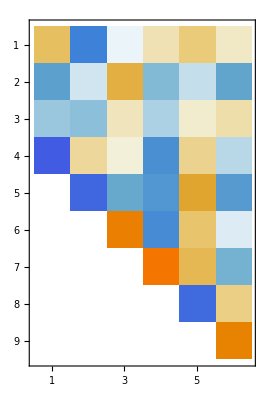

```mathematica
{m,b}={23,3};
A=RandomReal[{-1,1},{m,m}];
Q1= QRDecomposition[RandomReal[{-1,1},{m,b}]]⟦1⟧ᵀ;
AQ1=A.Q1;
H11=(Q1ᵀ.AQ1);
Q2=AQ1-Q1.H11;
{Q2,R21}= QRDecomposition[Q2];Q2=Q2ᵀ;
AQ2=A.Q2;
H12=(Q1ᵀ.AQ2);H22=(Q2ᵀ.AQ2);
Q3=AQ2-Q1.H12-Q2.H22;
{Q3,R32}= QRDecomposition[Q3];Q3=Q3ᵀ;
QQ2=ArrayFlatten[{{Q1,Q2}}];
QQ3=ArrayFlatten[{{Q1,Q2,Q3}}];
HH =ArrayFlatten[({{H11, H12}, {R21, H22}, {0, R32}})];
MatrixPlot[HH]
Norm[A.QQ2-QQ3.HH]
```

2.09319×10^-14

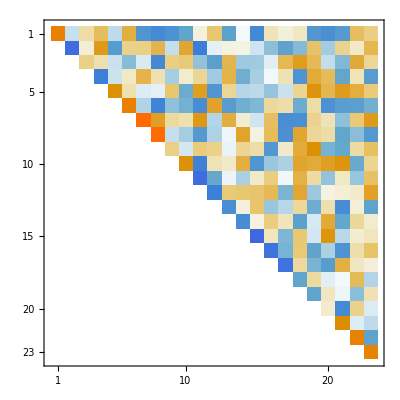

```mathematica
{Q,T}=SchurDecomposition[A,RealBlockDiagonalForm->False];
Norm[A-Q.T.ConjugateTranspose[Q]]
MatrixPlot[T]
```